```mathematica
K=1;
r=1;
λ = 1;
S = 1;
b = 1;
```

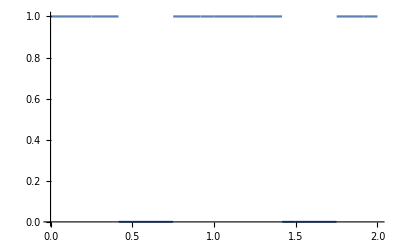

```mathematica
oneTo5[t_] :=HeavisideTheta[Sin[2π( t - 0/12)]]HeavisideTheta[-Sin[2π( t - 5/12)]];
tenTo12[t_]:=HeavisideTheta[Sin[2π( t - 9/12)]]HeavisideTheta[-Sin[2π( t - 12/12)]];
Plot[ oneTo5[t]+tenTo12[t],{t,0,2}]
```

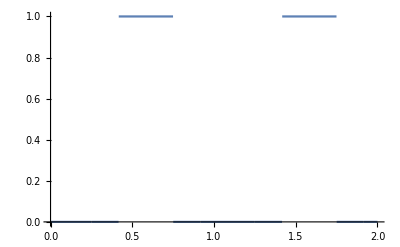

```mathematica
sixTo9[t_] := HeavisideTheta[Sin[2π( t - 5/12)]]HeavisideTheta[-Sin[2π( t - 9/12)]]
Plot[sixTo9[t],{t,0,2}]
```

```mathematica
eq1= x'[t]== r x[t] (1-x[t]/K)-b 1 x[t];
eq3= x'[t]== r x[t] (1-x[t]/K)-b S(oneTo5[t] + tenTo12[t]) x[t]^2/(1+x[t]^2);
sol1=NDSolve[{ eq1,x[0.001]==1},x,{t,0,30}]
sol3=NDSolve[{ eq3,x[0.001]==1},x,{t,0,30}]
r1 = 1;
r2 = 2; 
eq4 = x'[t]==(r1  x[t] (1-x[t]/K)-b  S (oneTo5[t] + tenTo12[t])x[t])(oneTo5[t] + tenTo12[t])+( r2 x[t] (1-x[t]/K)-b  S (oneTo5[t] + tenTo12[t]) x[t]) sixTo9[t]
sol4=NDSolve[{eq4,x[0.001]==1},x,{t,0.0,30}]
```

{{x→InterpolatingFunction[…]}}

{{x→InterpolatingFunction[…]}}

{{x[t]→1/(t-C[1])}}

x'[t]==(HeavisideTheta[-Sin[2 π (-1+t)]] HeavisideTheta[Sin[2 π (-3/4+t)]]+HeavisideTheta[-Sin[2 π (-5/12+t)]] HeavisideTheta[Sin[2 π t]]) (-((HeavisideTheta[-Sin[2 π (-1+t)]] HeavisideTheta[Sin[2 π (-3/4+t)]]+HeavisideTheta[-Sin[2 π (-5/12+t)]] HeavisideTheta[Sin[2 π t]]) x[t])+(1-x[t]) x[t])+HeavisideTheta[-Sin[2 π (-3/4+t)]] HeavisideTheta[Sin[2 π (-5/12+t)]] (-((HeavisideTheta[-Sin[2 π (-1+t)]] HeavisideTheta[Sin[2 π (-3/4+t)]]+HeavisideTheta[-Sin[2 π (-5/12+t)]] HeavisideTheta[Sin[2 π t]]) x[t])+2 (1-x[t]) x[t])

{{x→InterpolatingFunction[…]}}

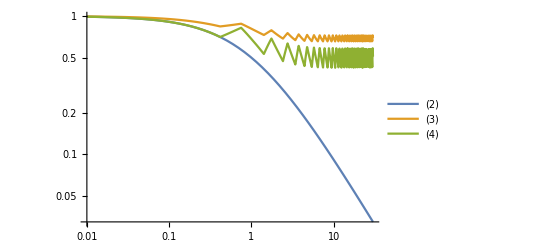

```mathematica
LogLogPlot[Evaluate[{x[t]/.sol1,x[t]/.sol3,x[t]/.sol4}],{t,0.01,30},PlotRange->All, PlotLegends->{"(2)","(3)","(4)"}]
```

```mathematica
αstar = 1;
βstar =1;
xstar = 1;
ϵ = 1;
P=1;
eq5 = {β'[t]==P - αstar (1-Exp[ϵ x[t]/xstar] )+ βstar (Exp[ϵ x[t]/xstar]-1)}
sol5=NDSolve[{eq3,eq5,x[0]==1,β[0]==1},{x,β},{t,0,30}]
```

{β'[t]==-1+2 ⅇ^x[t]}

{{x→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

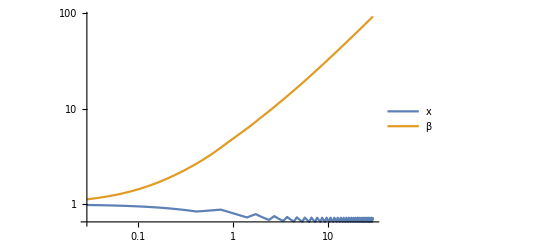

```mathematica
LogLogPlot[Evaluate[{x[t]/.sol5,β[t]/.sol5}],{t,0,30},PlotRange->All, PlotLegends->{"x","β"}]
```

方程(4)

```mathematica
eq1= x'[t]== r1 x[t] (1-x[t]/K)-b S x[t];
eq2 =
```